```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"qtools.wl"
<<"mathutils.m"
<<"MaTeX`"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*The physical properties of the manipulator. Assuming the legs to be solid rods of 10mm OD*)
```

```mathematica
leglparam = {ro->0.005, ri->0, ρ-> 7858, l->0.82, r->0.7};
legmparam = {mr-> ρ*π*(ro^2-ri^2)*r, ml-> ρ*π*(ro^2-ri^2)*l, g->9.8}/.leglparam;
ilzi =  ml*(ri^2+ro^2)/2;
ilxi = ml*(3*(ro^2+ri^2)+l^2)/12;
ilyi = ml*(3*(ro^2+ri^2)+l^2)/12;

irzi =  mr*(ri^2+ro^2)/2;
irxi = mr*(3*(ro^2+ri^2)+r^2)/12;
iryi = mr*(3*(ro^2+ri^2)+r^2)/12;
```

```mathematica
(*For the purpose of computation of inertia of the top plate assume that the top plate is regular. We know the Iz from https://en.wikipedia.org/wiki/List_of_moments_of_inertia and from perpendicular axis theorem we get itpx and itpy and assumed to be completely planar*)
```

```mathematica
(*Confirm the γt between my plate and Safar's plate*)
```

```mathematica
datap ={rb->1, rt->0.6, γt->0.4040437218366873, γb->0.8080874436733746};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 200+0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;
```

```mathematica
(*Inertias of the links. Assuming the manipulator is symmetric, and hence all the legs have the same inertia*)
```

```mathematica
Il ={{ilxi, 0, 0}, {0,ilyi, 0}, {0, 0,ilzi}};
Ir = {{irxi,0,0}, {0,iryi,0},{0,0,irzi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*Locations of all the known ground joints*)
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];
```

```mathematica
(*Locations of the top platform in local coordinates*)
```

```mathematica
al1 ={rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
```

```mathematica
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
```

```mathematica
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
```

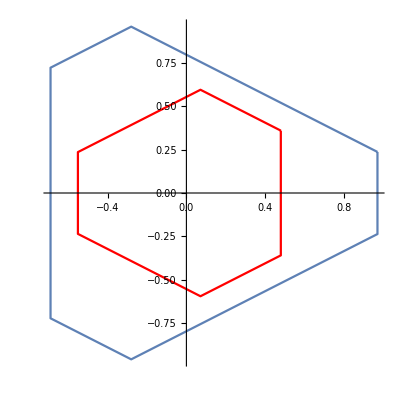

```mathematica
Show[ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]]],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Red], AspectRatio->1]
```

```mathematica
(*The method of formulation here is the Extended-Configuration-Space mapped to the Task-Space approach. Hence each of the body is described in its natural coordinates*)
```

```mathematica
(*The Cartesian coordinates of the center of the top plate*)
```

```mathematica
pc = {x, y, z};
```

```mathematica
(*The variables sets are*)
```

```mathematica
qx = Join[pc, {c1, c2, c3}];
qθ = Table[Symbol["θ"<>ToString[i]],{i, 6}];
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
qϕ = Join[ϕ, ψ];
q = Join[qx, qϕ, qθ];
```

```mathematica
(*Now the Jv and Jω of the top plate*)
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
```

```mathematica
(*Checking the orthogonolity of the rotation matrix*)
```

```mathematica
Simplify[Rtp.T[Rtp]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Jvtp = D[pc, {q}];
Jωtp = SkewMat2vec[Simplify[T[Rtp].D[Rtp,{q}]]];
```

```mathematica
(*Finding the Jvp for the links attached to the rotary joints*)
```

```mathematica
α = (2π/3-2*γb)/2;
```

```mathematica
raxis = {α+π/2,α+2*γb+π/2,3*α+2*γb+π/2,2π/3+2*γb+α+π/2,-α-2*γb+π/2,π/2-α};
```

```mathematica
pl= Table[b[[i]]+rotZ[raxis[[i]]].rotX[qθ[[i]]].{0, 0, l/2},{i, 6}];
pr = Table[b[[i]]+rotZ[raxis[[i]]].rotX[qθ[[i]]].{0, 0, l}+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, r/2},{i, 6}];
```

```mathematica
(*Checking the perpendicularity of the rotary joints*)
```

```mathematica
axis = Table[{Cos[raxis[[i]]], Sin[raxis[[i]]],0},{i,6}]/.datap;
Table[(rotZ[raxis[[i]]].{1,0,0}).b[[i]]/.datap,{i,6}]
```

{0.,-5.55112×10^-17,3.88578×10^-16,5.55112×10^-17,-2.22045×10^-16,-2.498×10^-16}

```mathematica
(*Linear velocity Jacobians*)
```

```mathematica
Jpl = D[pl, {q}];
Jpr = D[pr, {q}];
```

```mathematica
(*Rotation matris of the l-links*)
```

```mathematica
Rl = Table[rotZ[raxis[[i]]].rotX[qθ[[i]]],{i, 6}];
```

```mathematica
(*Rotation matrix of the r-links*)
```

```mathematica
Rr = Table[rotZ[raxis[[i]]].rotX[qθ[[i]]].rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
```

```mathematica
(*Angular velocity Jacobians of the links*)
```

```mathematica
Jωl = Table[SkewMat2vec[T[Rl[[i]]].D[Rl[[i]],{q}]],{i, 6}];
Jωr = Table[SkewMat2vec[T[Rr[[i]]].D[Rr[[i]],{q}]],{i, 6}];
```

```mathematica
(*Mass Matrix*)
```

```mathematica
tempM = Append[(Table[T[Jpl[[i]]].Jpl[[i]]*ml+T[Jpr[[i]]].Jpr[[i]]*mr+T[Jωl[[i]]].Il.Jωl[[i]]+T[Jωr[[i]]].Ir.Jωr[[i]],{i, 6}]), T[Jvtp].Jvtp*mtp+T[Jωtp].Itp.Jωtp];
tempM//dim
```

{7,24,24}

```mathematica
tempM2 = Total[tempM, {1}];
tempM2//dim
```

{24,24}

```mathematica
(*Verifying the properties of the Mass Matrix*)
```

```mathematica
(*tempM2 - T[tempM2]*)
```

```mathematica
(*Changing Mmat for deriving Cmat*)
```

```mathematica
qθrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], qθ[[i]]->qθ[[i]][t]},{i, 6}]];
qxrule = {x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]};
```

```mathematica
qrule = Join[qθrule, qxrule];
```

```mathematica
tic[]
Mmat = Simplify[tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam];
toc[]
```

Actual time consumed: 13.20569 seconds.

CPU time consumed: 13.5549 seconds.

```mathematica
qt = q/.qrule;
```

```mathematica
(*Deriving the Cmat from the Mmat*)
```

```mathematica
tic[]
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii= 1, ii≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.21384 seconds.

CPU time consumed: 0.210029 seconds.

```mathematica
(*Verifying the property of Cmat*)
```

```mathematica
(*dMmat = D[Mmat, t];
tempA = dMmat-2*tempC;
temppA = tempA+T[tempA];
temppA//dim
Chop[Simplify[temppA]]*)
```

```mathematica
(*Formulating the potential energy term*)
```

```mathematica
tempV = Table[ml*g*pl[[i]][[3]]+mr*g*pr[[i]][[3]],{i, 6}];
V = Total[Append[Flatten[tempV], mtp*g*pc[[3]]]]/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V,{q}];
```

```mathematica
(*Formulating the top platform coordinates in two paths*)
```

```mathematica
ptopendtp = Table[pc+Rtp.al[[i]],{i,6}];
ptopendj = Table[b[[i]]+rotZ[raxis[[i]]].rotX[qθ[[i]]].{0, 0, l}+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, r},{i, 6}];
pairend = Table[b[[i]]+rotZ[raxis[[i]]].rotX[qθ[[i]]].{0, 0, l},{i, 6}];
```

```mathematica
(*Formulating the simpler form of the 18 constraints*)
```

```mathematica
(*We go to the vertices of the hexagon from the global from via links and via the top platform and constraint thier x,y,z coordintaes*)
```

```mathematica
η = Numerator[Simplify[Together[Flatten[ptopendj-ptopendtp]]]];
```

```mathematica
(* denη = Denominator[Simplify[Together[Flatten[ptopend-ptopend2]]]];*)
```

```mathematica
(*So we assume that 1+c1^2+c2^2+c3^2 is non zero*)
```

```mathematica
(*η//Dimensions*)
```

```mathematica
(*Now we need to map these matrices from extended configuration space to the required space, which in this case is task space*)
```

```mathematica
qq  =Join[qϕ, qθ];
```

```mathematica
Jηq = D[η,{qq}];
Jηx = D[η, {qx}];
```

```mathematica
(*Assuming the working of the manipulator in SWZ and also not having Jηq singularity anywhere. Interesting that this map demands Jηq Jacobians existence and not Jηϕ*)
```

```mathematica
plist = Table[Symbol["p"<>ToString[i]],{i, 6}];
slist = Table[Symbol["s"<>ToString[i]],{i, 6}];
hlist = Table[Symbol["h"<>ToString[i]],{i, 6}];
```

```mathematica
qqlist = Join[plist, slist, hlist];
```

```mathematica
dϕ = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["ds"<>ToString[i]],{i, 6}];
dθ = Table[Symbol["dh"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dθ];
dqrule = Inner[Rule, D[qq/.qrule, t], dq, List];
rqqrule= Join[Inner[Rule,qq/.qrule, qqlist, List], dqrule];
rxrule = Inner[Rule, qx/.qrule, qx, List];
drxrule = Inner[Rule, D[qx/.qrule, t], {dx, dy, dz, dc1, dc2, dc3}, List];
rqrule = Join[rxrule, drxrule, rqqrule];
```

```mathematica
(*Converting the time dendent functions to variables for compilation*)
```

```mathematica
tJηq = Jηq/.qrule/.rqrule/.leglparam/.datap;
```

```mathematica
cJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tJηq]];
```

```mathematica
dJηq = D[Jηq/.qrule, t]/.rqrule/.leglparam/.datap;
```

```mathematica
cdJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dp1, _Real},{dp2, _Real},{dp3, _Real},{dp4, _Real},{dp5, _Real},{dp6, _Real},{ds1, _Real},{ds2, _Real},{ds3, _Real},{ds4, _Real},{ds5, _Real},{ds6, _Real},{dh1, _Real},{dh2, _Real},{dh3, _Real},{dh4, _Real},{dh5, _Real},{dh6, _Real}}, Evaluate[dJηq]];
```

```mathematica
tJηx = Jηx/.qrule/.rqrule/.leglparam/.datap;
```

```mathematica
cJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tJηx]];
```

```mathematica
dJηx = D[Jηx/.qrule, t]/.rqrule/.leglparam/.datap;
```

```mathematica
cdJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dp1, _Real},{dp2, _Real},{dp3, _Real},{dp4, _Real},{dp5, _Real},{dp6, _Real},{ds1, _Real},{ds2, _Real},{ds3, _Real},{ds4, _Real},{ds5, _Real},{ds6, _Real},{dh1, _Real},{dh2, _Real},{dh3, _Real},{dh4, _Real},{dh5, _Real},{dh6, _Real}}, Evaluate[dJηx]];
```

```mathematica
(*Compiling the coefficients matrices of the dynamics equations*)
```

```mathematica
tMmat = TrigExpand[Mmat/.rqrule];
```

```mathematica
cMmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tMmat]];
```

```mathematica
tCmat = TrigExpand[tempC/.rqrule];
```

```mathematica
cCmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dp1, _Real},{dp2, _Real},{dp3, _Real},{dp4, _Real},{dp5, _Real},{dp6, _Real},{ds1, _Real},{ds2, _Real},{ds3, _Real},{ds4, _Real},{ds5, _Real},{ds6, _Real},{dh1, _Real},{dh2, _Real},{dh3, _Real},{dh4, _Real},{dh5, _Real},{dh6, _Real}}, Evaluate[tCmat]];
```

```mathematica
tGvec = TrigExpand[G/.qrule/.rqrule];
```

```mathematica
cGvec = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tGvec]];
```

```mathematica
(*IK module for the manipulator*)
```

```mathematica
(*Constraining the length of r-link*)
```

```mathematica
rconst = Table[Expand[(ptopendtp[[i]]-pairend[[i]]).(ptopendtp[[i]]-pairend[[i]])-r^2],{i,6}];
```

```mathematica
tempθsol = Table[solveLinTrig1[Numerator[Together[rconst[[i]]]], qθ[[i]]],{i, 6}];
```

```mathematica
(*Now from the known values of θ. Extracting the ϕ and ψ*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
rjoints = {rj1, rj2, rj3, rj4, rj5, rj6};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
rjointrules = Inner[Rule, rjoints, raxis, List];
backrules = Join[alsrules, bsrules, rjointrules];
```

```mathematica
ptopendtps = Table[pc+Rtp.als[[i]],{i,6}];
ptopendjs = Table[bs[[i]]+rotZ[rjoints[[i]]].rotX[qθ[[i]]].{0, 0, l}+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, r},{i, 6}];
pairends = Table[bs[[i]]+rotZ[rjoints[[i]]].rotX[qθ[[i]]].{0, 0, l},{i, 6}];
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
cosψ= Table[Solve[Simplify[Numerator[Together[Expand[((ptopendtps[[i]][[1]]-bs[[i]][[1]]-l*Sin[rjoints[[i]]]*Sin[qθ[[i]]])/(r*Cos[ψ[[i]]]))^2+((ptopendtps[[i]][[3]]-l*Cos[qθ[[i]]])/(r*Cos[ψ[[i]]]))^2-1]]]]==0, Cos[ψ[[i]]]],{i,6}]/.backrules/.leglparam/.datap;
```

```mathematica
sinψ = Table[Simplify[Together[Expand[(ptopendtps[[i]][[2]]-bs[[i]][[2]]+l*Cos[rjoints[[i]]]*Sin[qθ[[i]]])/(-r)]]],{i, 6}]/.backrules/.leglparam/.datap;
```

```mathematica
cosϕ = Table[Simplify[Together[(ptopendtps[[i]][[3]]-l*Cos[qθ[[i]]])/(r*Cos[ψ[[i]]])]],{i,6}]/.backrules/.leglparam/.datap;
```

```mathematica
sinϕ = Table[Simplify[Together[(ptopendtps[[i]][[1]]-bs[[i]][[1]]-l*Sin[rjoints[[i]]]*Sin[qθ[[i]]])/(r*Cos[ψ[[i]]])]],{i,6}]/.backrules/.leglparam/.datap;
```

```mathematica
θsol = tempθsol/.leglparam/.datap;
```

```mathematica
(*These give us the IK solutions. Now testing with a sample configuration*)
```

```mathematica
(*Let us consider a symmetric pose to determine the IK branch we would like to choose. Please note that we disregard the collision between the links here*)
```

```mathematica
samplex = {x->0, y->0, z->0.75, c1->0, c2->0, c3->0}
```

{x→0,y→0,z→0.75,c1→0,c2→0,c3→0}

```mathematica
tempθsamp = θsol/.samplex;
```

```mathematica
Table[(qθ[[i]]/.tempθsamp[[i]])*(180/π),{i,6}]//mf
```

(14.7919 | 283.47
14.7919 | 283.47
14.7919 | 283.47
14.7919 | 283.47
14.7919 | 283.47
14.7919 | 283.47)

```mathematica
(*From observation the first branch for θ is selected for all the θ's*)
```

```mathematica
tempθsolb1 = Flatten[Table[θsol[[i]][[1]],{i,6}]];
```

```mathematica
θsolb1 = qθ/.tempθsolb1;
```

```mathematica
tempcosψ = Table[Cos[ψ[[i]]]/.cosψ[[i]],{i,6}];
```

```mathematica
(*From the values we choose the second set of solutions for cosψ. Though this doesnt really give a different solution*)
```

```mathematica
cosψb1 = tempcosψ[[;;,2]];
```

```mathematica
ψsol = Table[ArcTan[cosψb1[[i]], sinψ[[i]]],{i,6}];
```

```mathematica
ϕsol = Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}];
```

```mathematica
(*Module for computing the IK of the manipulator*)
```

```mathematica
θsolrule = Inner[Rule,qθ,θsolb1,List];
ψsolrule = Inner[Rule,ψ,ψsol, List];
ϕsolrule = Inner[Rule,ϕ,ϕsol, List];
```

```mathematica
(*Now finding the values of the other variables for this symmetric configuration*)
```

```mathematica
θtest = θsolrule/.samplex/.datap/.leglparam
```

{θ1→0.258167,θ2→0.258167,θ3→0.258167,θ4→0.258167,θ5→0.258167,θ6→0.258167}

```mathematica
ψtest = ψsolrule/.samplex/.leglparam/.θtest
```

{ψ1→-0.105068,ψ2→0.939361,ψ3→1.14827,ψ4→-1.14827,ψ5→-0.939361,ψ6→0.105068}

```mathematica
ϕtest = ϕsolrule/.samplex/.leglparam/.θtest/.ψtest
```

{ϕ1→-1.63235,ϕ2→1.67462,ϕ3→1.72055,ϕ4→1.72055,ϕ5→1.67462,ϕ6→-1.63235}

```mathematica
ψsolrule2 = Inner[Rule,ψ,ψsol, List]/.θsolrule;
ϕsolrule2 = Inner[Rule,ϕ,ϕsol, List]/.θsolrule/.ψsolrule2;
```

```mathematica
cθsol = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[qq[[-6;;]]/.θsolrule]];
```

```mathematica
cψsol = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {θ1, _Real},{θ2, _Real},{θ3, _Real},{θ4, _Real},{θ5, _Real},{θ6, _Real}}, Evaluate[ψsol]];
```

```mathematica
cϕsol = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {θ1, _Real},{θ2, _Real},{θ3, _Real},{θ4, _Real},{θ5, _Real},{θ6, _Real}, {ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[qq[[;;6]]/.ϕsolrule]];
```

```mathematica
iksol[x_]:=Module[{θval, ψval, ϕval},
θval = cθsol@@x;
ψval =cψsol@@Join[x, θval];
ϕval =cϕsol@@Join[x, θval, ψval];
Return[Join[ϕval, ψval, θval]];
]
```

```mathematica
iksolmod[x_]:=Module[{θval, ψval, ϕval},
θval = cθsol@@x;
ψval =cψsol@@Join[x, θval];
ϕval =cϕsol@@Join[x, θval, ψval];
Return[Join[ϕval, ψval, θval]];
]
```

```mathematica
(*Now let us check the constraints for this configuration*)
```

```mathematica
Chop[η/.Inner[Rule, qq, iksol/.samplex,List]/.leglparam/.datap/.samplex]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Therefore the obtained configuration is feasible*)
```

```mathematica
ciksol = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[iksol]];
```

```mathematica
(*Initial solutions*)
```

```mathematica
qxinit = qx/.samplex;
dqxinit = {0,0,0,0,0,0};
```

```mathematica
qeinit = Join[qxinit, iksolmod[qxinit]];
dqeinit = ConstantArray[0, 24];
```

```mathematica
(*The equations of motion are*)
```

```mathematica
doubledots[iq_?(VectorQ[#,NumericQ]&),diq_?(VectorQ[#,NumericQ]&)]:=Module[{q, dq, Mval, Cval, Gval, LHS, Mxval, Cxval, Gxval, Jηxval, Jηqval, Jqxval, dqe, qe, dJηqval, dJηxval, Jqexval, dJqexval},
(*q = Chop[Re[iq]];
dq = Chop[Re[diq]];*)
q = iq;
dq = diq;
(*Perform the IK for the configuration variables*)
(*qe = Join[q, ciksol@@q];*)
qe = Join[q, iksolmod[q]];
(*Getting the velocities of the configuration space variables*)
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dq, Jqxval.dq];
(*Compute all the coefficient matrices in the extended configuration space*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
Jqexval = ArrayFlatten[{{IdentityMatrix[6]}, {Jqxval}}];
dJqexval = ArrayFlatten[{{ConstantArray[0, {6, 6}]}, {-Inverse[Jηqval].(-dJηqval.Inverse[Jηqval].Jηxval+dJηxval)}}];
(*Map the matrices to the task space*)
Mxval = T[Jqexval].Mval.Jqexval;
Cxval = T[Jqexval].(Mval.dJqexval+Cval.Jqexval);
Gxval = T[Jqexval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mxval]).(Cxval.dq+Gxval);
Return[LHS];
];
```

```mathematica
iksolmod[{0.1,0.1,1,0.1,0.1,-0.1}]
```

{-1.25837,1.1336,0.876426,0.526897,1.37607,-1.50822,-0.0633113,0.434548,0.648744,-1.12482,-1.02234,0.0594925,0.429253,-0.00638906,0.209165,-0.103283,0.156427,0.267356}

```mathematica
tf = 0.6;
tic[]
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]=={0.1,0.1,1,0.1,0.1,-0.1},q1'[0]==dqxinit},q1,{t,0,tf}(*, Method->"Adams", AccuracyGoal->15*)]
toc[]
```

{{q1→InterpolatingFunction[…]}}

Actual time consumed: 0.38411 seconds.

CPU time consumed: 0.356506 seconds.

```mathematica
(*Now performing the energy checks needed*)
```

```mathematica
qsol = (q1/.dynsim)[[1]];
```

```mathematica
(*Plotting the manipulator as it moves*)
```

```mathematica
qvals = Table[Inner[Rule, q, Join[qsol[i],iksolmod[qsol[i]]], List],{i, 0,tf, 0.001}];
```

```mathematica
(*Plotter*)
```

```mathematica
plot6rss[qvals_]:=Module[{base, top, llinks, rlinks, jointsbase, jointstop, jointsair,jlist,bval,aval,pairendval, aa},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[ptopendtp/.datap/.leglparam];
pairendval = pairend/.datap/.leglparam;
aa = 2.5;
base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-aa,aa}, {-aa,aa}, {-aa,aa}}];
top = Graphics3D[{Gray,Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],pairendval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];
rlinks = Table[Graphics3D[{Orange,Opacity[0.5],Cylinder[{pairendval[[i]]/.qvals, aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];
(*Joints*)
jlist = Table[{Cos[raxis[[i]]], Sin[raxis[[i]]],0},{i,6}]/.datap;
jointsbase = Table[Graphics3D[{Black,Cylinder[{(bval[[i]]+0.15*jlist[[i]]), (bval[[i]]-0.15*jlist[[i]])}, 0.05]}],{i, Length[bval]}];
jointsair = Table[Graphics3D[Sphere[pairendval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, llinks, rlinks, jointsair, jointstop, jointsbase]
]
```

```mathematica
man6rss = Manipulate[
plot6rss[qvals[[j]]],
{j, 1, Length[qvals], 1}]
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize, PlotRange->All];

Return[f1nonsing];
]
```

```mathematica
(*loop closure in completely task space variables*)
ηeqn = η/.datap/.leglparam;
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
time = Table[t,{t,0, 0.3,0.01}];
```

```mathematica
(*ηtest = Table[Max[Abs[ηeqn/.Inner[Rule, q, Join[qsol[i],ciksol@@qsol[i]],List]]],{i, 0, 0.3, 0.01}];
Texplot[time, ηtest*10^15, 800, "Time~(s)", "e_1 (\\times 10^{-15})"]*)
```

CompiledFunction::cfse: Compiled expression iksol should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

CompiledFunction::cfse: Compiled expression iksol should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.100001,0.0999998,0.999509,0.100023,0.10001,-0.100023},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Inner::heads will be suppressed during this calculation.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.100005,0.0999994,0.998038,0.100092,0.100041,-0.100092},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.100001,0.0999998,0.999509,0.100023,0.10001,-0.100023},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Inner::heads will be suppressed during this calculation.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.100005,0.0999994,0.998038,0.100092,0.100041,-0.100092},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
```

```mathematica
Jηqe = D[ηeqn,{q}]/.qrule/.rqrule;
```

```mathematica
cJηqe = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[Jηqe]];
```

```mathematica
(*We need to find the velocities of the configuration variables*)
```

```mathematica
dqemod[qx_, dqx_] := Module[{qde, Jηqval, Jηxval, Jqxval, dqe, qe},
qe = Join[qx, ciksol@@qx];
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dqx, Jqxval.dqx];
Return[dqe]
]
```

```mathematica
(*Jηqetest = Table[Max[Abs[(cJηqe@@Join[qsol[i], iksolmod[qsol[i]]]).Chop[dqemod[qsol[i],qsol'[i]]]]],{i, 0, 0.3, 0.01}];
Texplot[time,Jηqetest*10^15, 800, "Time~(s)", "e_2 (\\times 10^{-15})"]*)
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 32 of {1000000000000000 Abs[{{-1.03,0.,0.,-0.0603243,0.131726,0.515974,0.221167,0.,0.,0.,«14»},{0.,-2.06,0.,0.0566649,-0.231202,-2.16921,0.,0.,0.,0.,«14»},{0.,0.,-1.03,-0.631575,1.02428,-0.160058,0.684723,0.,0.,0.,«14»},«5»,{0.,0.,-1.03,-0.550293,-1.02439,0.031349,0.,0.,-0.441497,0.,«14»},{-1.03,0.,0.,0.0413851,-0.17929,-0.245301,0.,0.,0.,0.268813,«14»},«8»}.Join[{«1»},«1»]],«10»} does not exist.

Part::partw: Part 33 of {1000000000000000 Abs[{{-1.03,0.,0.,-0.0603243,0.131726,0.515974,0.221167,0.,0.,0.,«14»},{0.,-2.06,0.,0.0566649,-0.231202,-2.16921,0.,0.,0.,0.,«14»},{0.,0.,-1.03,-0.631575,1.02428,-0.160058,0.684723,0.,0.,0.,«14»},«5»,{0.,0.,-1.03,-0.550293,-1.02439,0.031349,0.,0.,-0.441497,0.,«14»},{-1.03,0.,0.,0.0413851,-0.17929,-0.245301,0.,0.,0.,0.268813,«14»},«8»}.Join[{«1»},«1»]],«10»} does not exist.

Part::partw: Part 34 of {1000000000000000 Abs[{{-1.03,0.,0.,-0.0603243,0.131726,0.515974,0.221167,0.,0.,0.,«14»},{0.,-2.06,0.,0.0566649,-0.231202,-2.16921,0.,0.,0.,0.,«14»},{0.,0.,-1.03,-0.631575,1.02428,-0.160058,0.684723,0.,0.,0.,«14»},«5»,{0.,0.,-1.03,-0.550293,-1.02439,0.031349,0.,0.,-0.441497,0.,«14»},{-1.03,0.,0.,0.0413851,-0.17929,-0.245301,0.,0.,0.,0.268813,«14»},«8»}.Join[{«1»},«1»]],«10»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$Aborted

```mathematica
(*Finding the same from the numerical deriivative of η*)
```

```mathematica
(*dηtest = DerivativeFilter[ηtest,{1}];*)
```

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Inner::heads will be suppressed during this calculation.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*ListLinePlot[dηtest,PlotRange->All]*)
```

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,«14»},Join[{0.1,0.1,1.,0.1,0.1,-0.1},iksol],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
```

```mathematica
(*Instead of finding the second derivative of the loop closure, finding it from the differences of the first order data*)
```

```mathematica
(*d2ηtest = DerivativeFilter[Jηqetest,{1}];
Texplot[time,d2ηtest*10^15, 800, "Time~(s)", "e_3 (\\times 10^{-15})"]*)
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

-Graphics-

```mathematica
(*To check Energy remove the applied external torque*)
```

```mathematica
(*4. Energy: Checking Energy constant criteria*)
```

```mathematica
(*PE = V/.qrule/.rqrule/.leglparam/.datap;
cPE = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[PE]];
Vlist = Table[cPE@@Join[qsol[i],ciksol@@qsol[i]],{i, 0,0.3, 0.001}];
Mlist = Table[Chop[cMmat@@Join[qsol[i],ciksol@@qsol[i]]],{i, 0,0.3, 0.001}];
dqlist = Table[Chop[dqemod[qsol[i], qsol'[i]]],{i, 0, 0.3, 0.001}];
Hlist = Table[1/2*(dqlist[[i]].Mlist[[i]].dqlist[[i]])+Vlist[[i]],{i, Length[dqlist]}];
H1 = ConstantArray[Hlist[[1]], Dimensions[Hlist]];*)
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

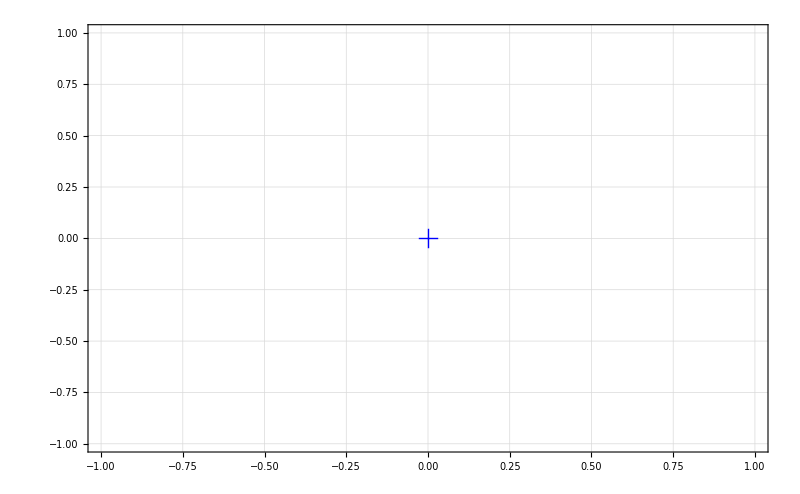

```mathematica
(*Texplot[time,(Hlist-H1)/H1*10^8, 800, "Time~(s)", "en (\\times 10^{-8})"]*)
```

```mathematica
(*ListLinePlot[(Hlist-H1)/H1, PlotRange->All]*)
```

Join::heads: Heads List and Dot at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
(*ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"test.avi"}],man],"ImageList"][[1;;-1;;step]]];*)
```

```mathematica
(*ManToGif[man6rss,FileNameJoin[{NotebookDirectory[],"test"}],1];*)
```

```mathematica
(*Constraints in joint space only*)
```

```mathematica
(*Formulating the 12 constraints of the top platform*)
```

```mathematica
a = Table[b[[i]]+rotZ[raxis[[i]]].rotX[qθ[[i]]].{0, 0, l}+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, r},{i, 6}];
```

```mathematica
ηtp= Join[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]], {Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])], Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])], Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])], Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
ηtp//Dimensions
```

{12}

```mathematica
tempJηϕ = D[ηtp, {Join[ϕ, ψ]}];
```

```mathematica
Det[tempJηϕ/.datap/.leglparam/.qvals[[-1]]];
```

```mathematica
(*The det is not zero, which means that the system becomes stiff not neccessarily due to singularity*)
```

```mathematica
(*Inverse Dynamics*)
```

```mathematica
(*Selecting the region for heave motion*)
```

```mathematica
tempqval = Join[{0,0,0.8,0,0,0}, iksolmod[{0,0,0.8,0,0,0}]];
plot6rss[Inner[Rule, q, tempqval,List]]
```

-Graphics3D-

```mathematica
(*Finding the required torques for 0.3g max acceleration. Heaving between 0.5-0.8. Since we have four constraints on initial positions and velocities, we have a 4th order polynomial*)
```

```mathematica
tempztraj = k1*t^3+k2*t^2+k3*t+k4;
tempdztraj = D[tempztraj,t];
```

```mathematica
(*Conditions on initial and final velocities, i.e. move from rest to rest*)
```

```mathematica
Clear[tf]
```

```mathematica
k1k2sol = Solve[{((tempztraj/.t->tf)-zf),(tempdztraj/.t->tf)}==0, {k1, k2}][[1]];
k4sol = Solve[((tempztraj/.t->0)-zi)==0, k4][[1]];
k3sol = Solve[(tempdztraj/.t->0)==0, k3][[1]];
```

```mathematica
temp2ztraj = Together[tempztraj/.k1k2sol/.k4sol/.k3sol];
zdat = {zi->0.3,zf->0.4, amax->0.8*g}/.g->9.8;
```

```mathematica
maxa = D[temp2ztraj,{t,2}];
```

```mathematica
tfsol= NSolve[((maxa/.zdat/.t->0)-amax)==0, tf][[2]]/.zdat;
```

```mathematica
ztraj = temp2ztraj/.zdat/.tfsol;
```

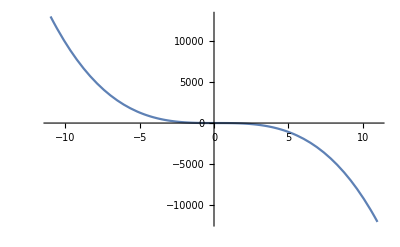

```mathematica
Plot[ztraj, {t, -11, 11}]
```

```mathematica
(*Now generate data for this z-trajectory, keeping the orientation of the top platform constant and {c1,c2,c3}={0,0,0}*)
```

```mathematica
hval = 0.01;
time = Table[i, {i,0,3*tf/.tfsol, hval}];
tempxdat = Table[{0,0,ztraj/.t->i,0,0,0}, {i,0,tf/.tfsol, hval}];
tempdxdat = Table[{0,0,D[ztraj,t]/.t->i,0,0,0}, {i,0,tf/.tfsol, hval}];
tempd2xdat = Table[{0,0,D[ztraj,{t,2}]/.t->i,0,0,0}, {i,0,tf/.tfsol, hval}];
```

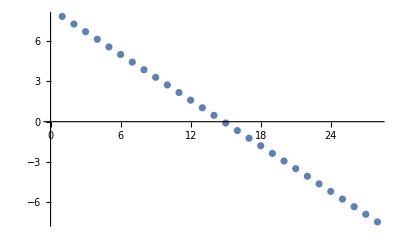

```mathematica
ListPlot[Table[tempd2xdat[[i]][[3]], {i, Length[tempd2xdat]}]]
```

```mathematica
(*Now since the motion is symmetric we can simply reverse it and append it to generate an SHM data*)
```

```mathematica
xdat = Join[tempxdat[[;;-2,;;]], Reverse[tempxdat],tempxdat[[2;;,;;]]];
dxdat = Join[tempdxdat[[;;-2,;;]], Reverse[tempdxdat],tempdxdat[[2;;,;;]]];
d2xdat = Join[tempd2xdat[[;;-2,;;]], Reverse[tempd2xdat],tempd2xdat[[2;;,;;]]];
```

```mathematica
(*Since we want to find the torques at each of the motor for this heave motion we have to map this dynamics to the actuator space. This is one of the advantages of formulation in extended task space. The formulation can be mapped to either task space or actuator space.*)
```

```mathematica
(*Formulating the Jacobians for mapping the dynamics to actuator space*)
```

```mathematica
Jηθ = D[ηeqn,{qθ}];
Jηϕx = D[ηeqn,{Join[qx,qϕ]}];
```

```mathematica
(*Converting the time dendent functions to variables for compilation*)
```

```mathematica
tJηθ = Jηθ/.qrule/.rqrule;
```

```mathematica
cJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tJηθ]];
```

```mathematica
dJηθ = D[Jηθ/.qrule, t]/.rqrule;
```

```mathematica
cdJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dp1, _Real},{dp2, _Real},{dp3, _Real},{dp4, _Real},{dp5, _Real},{dp6, _Real},{ds1, _Real},{ds2, _Real},{ds3, _Real},{ds4, _Real},{ds5, _Real},{ds6, _Real},{dh1, _Real},{dh2, _Real},{dh3, _Real},{dh4, _Real},{dh5, _Real},{dh6, _Real}}, Evaluate[dJηθ]];
```

```mathematica
tJηϕx = Jηϕx/.qrule/.rqrule;
```

```mathematica
cJηϕx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}}, Evaluate[tJηϕx]];
```

```mathematica
dJηϕx = D[Jηϕx/.qrule, t]/.rqrule;
```

```mathematica
cdJηϕx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {p1, _Real},{p2, _Real},{p3, _Real},{p4, _Real},{p5, _Real},{p6, _Real},{s1, _Real},{s2, _Real},{s3, _Real},{s4, _Real},{s5, _Real},{s6, _Real},{h1, _Real},{h2, _Real},{h3, _Real},{h4, _Real},{h5, _Real},{h6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dp1, _Real},{dp2, _Real},{dp3, _Real},{dp4, _Real},{dp5, _Real},{dp6, _Real},{ds1, _Real},{ds2, _Real},{ds3, _Real},{ds4, _Real},{ds5, _Real},{ds6, _Real},{dh1, _Real},{dh2, _Real},{dh3, _Real},{dh4, _Real},{dh5, _Real},{dh6, _Real}}, Evaluate[dJηϕx]];
```

```mathematica
(*Computing the joint space data from the task space data*)
```

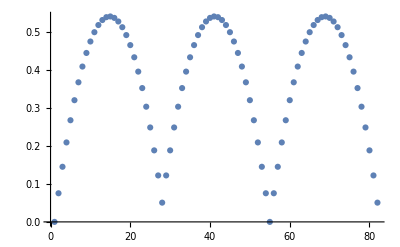

```mathematica
ListPlot[Table[dxdat[[i]][[3]], {i, Length[xdat]}]]
```

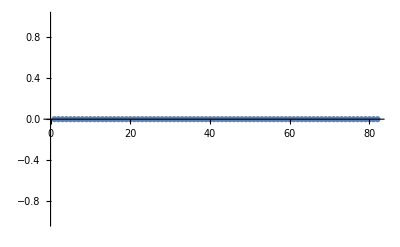

```mathematica
ListPlot[Table[dxdat[[i]][[2]], {i, Length[xdat]}]]
```

```mathematica
qedat = Table[Join[xdat[[i]],iksolmod[xdat[[i]]]],{i,Length[xdat]}];
dqedat = Table[Join[dxdat[[i]], -Inverse[(cJηq@@qedat[[i]])].(cJηx@@qedat[[i]]).dxdat[[i]]],{i, Length[dxdat]}];
d2qedat=Table[Join[d2xdat[[i]], -Inverse[(cJηq@@qedat[[i]])].(cJηx@@qedat[[i]]).d2xdat[[i]]+(-Inverse[cJηq@@qedat[[i]]].(-cdJηq@@Join[qedat[[i]], dqedat[[i]]].Inverse[cJηq@@qedat[[i]]].cJηx@@qedat[[i]]+cdJηx@@Join[qedat[[i]], dqedat[[i]]])).d2xdat[[i]]],{i, Length[d2xdat]}];
d2θdat = d2qedat[[;;,19;;24]];
```

```mathematica
(*Implementing actuator space ID*)
```

```mathematica
ID[qe_?(VectorQ[#,NumericQ]&),dqe_?(VectorQ[#,NumericQ]&),d2θ_?(VectorQ[#,NumericQ]&)]:=Module[{q, dq, Mval, Cval, Gval, τθ, Mθval, Cθval, Gθval, Jηθval, Jηxϕval, Jxϕθval, dJηxϕval, dJηθval, Jqeθval, dJqeθval, dθ},
(*Getting the velocities of the configuration space variables*)
dθ = dqe[[19;;24]];
Jηxϕval = cJηϕx@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
(*Compute all the coefficient matrices in the extended configuration space*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηϕx@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval},{IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)},{ConstantArray[0, {6, 6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*Inverse Dynamics*)
τθ = Mθval.d2θ+Cθval.dθ+Gθval;
Return[τθ];
];
```

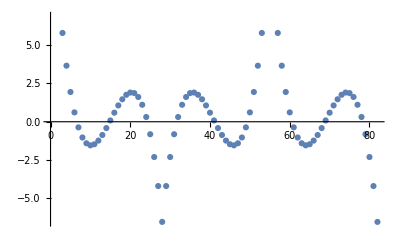

```mathematica
ListPlot[d2θdat[[;;,1]]]
```

```mathematica
tic[]
τθdat = Table[Chop[ID[qedat[[i]], dqedat[[i]],d2θdat[[i]]]],{i, Length[d2xdat]}];
toc[]
```

Actual time consumed: 0.11551 seconds.

CPU time consumed: 0.115119 seconds.

```mathematica
μτθ = Table[{time[[i]], Mean[τθdat[[i]]]},{i, Length[d2xdat]}];
```

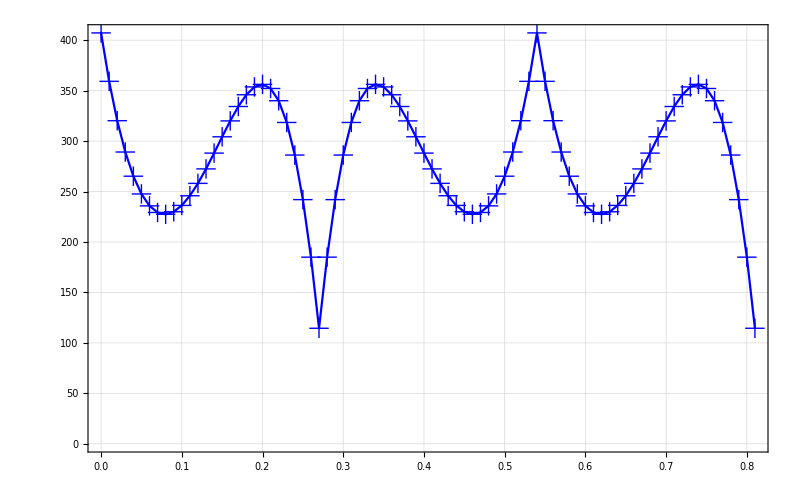

```mathematica
Texplot[μτθ[[;;,1]], μτθ[[;;,2]], 800, "Time~(s)", "\\textrm{Torque (N-m)}"]
```

```mathematica
man6rss = Manipulate[
plot6rss[Inner[Rule, q,qedat[[j]],List]],
{j, 1, Length[qedat], 1}, ContentSize->{400,400}]
```

```mathematica
(*frames = Table[Export["6rss"<>ToString[j]<>".jpeg", plot6rss[Inner[Rule, q,qedat[[j]],List]]],{j, 1, 84, 1}];*)
```

```mathematica
(*Formulating the extended to actuator space dynamics to enable control*)
```

```mathematica
(*Or can experiment to have the dynamics in task space and just map the motor torques form the motors to the end-effector *)
```

```mathematica
(*trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};


inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
Print["Change the angles from Greek symbols"]*)
```

Change the angles from Greek symbols

```mathematica
(*phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];*)
```

```mathematica
(*cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
costh = Table[Symbol["ch"<>ToString[i]],{i, 6}];
sinth = Table[Symbol["sh"<>ToString[i]],{i, 6}];*)
```

```mathematica
(*trigtoalg = Join[Inner[Rule, Cos[slist], cospsi, List], Inner[Rule, Sin[slist], sinpsi, List], Inner[Rule, Cos[plist], cosphi, List],    Inner[Rule, Sin[plist], sinphi, List],Inner[Rule, Cos[hlist], costh, List], Inner[Rule, Sin[hlist], sinth, List]];*)
```

```mathematica
(*PortMattoC[mat_]:=Module[{tempMattoC, mattoC},
(*Substitute all Greek letters and flatten matrices into vectors*)
tempMattoC = Flatten[mat]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = StringTake[ToString[Table[CForm[tempMattoC[[i]]],{i, Length[tempMattoC]}]],{2,-2}];
Return [mattoC];
]*)
```

```mathematica
(*MmattoC = PortMattoC[tMmat];
CmattoC = PortMattoC[tCmat];
GmattoC = PortMattoC[tGvec];*)
```

```mathematica
(*JηqqtoC = PortMattoC[tJηq];
JηqxtoC = PortMattoC[tJηx];*)
```

```mathematica
(*dJηqqtoC = PortMattoC[dJηq];
dJηqxtoC = PortMattoC[dJηx];*)
```

```mathematica
(*newrule = qrule/.rqrule;*)
```

```mathematica
(*SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];*)
```

```mathematica
(*$PrePrint=#/.{Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;*)
```

```mathematica
(*Unprotect[Csc,Sec];
Format[Csc[x_]]:=HoldForm[1/Sin[x]];
Format[Sec[x_]]:=HoldForm[1/Cos[x]];
Protect[Csc,Sec];*)
```

```mathematica
(*(*Cos psi in phval doesnt change and so it is computed twice than once*)
θvaltoC = PortMattoC[qq[[-6;;]]/.θsolrule];
ψvaltoC = PortMattoC[ψsol/.newrule];
ϕvaltoC = PortMattoC[qq[[;;6]]/.ϕsolrule/.newrule];*)
```

```mathematica
(*file = Import["dyn_funcs.h", "Text"];*)
```

```mathematica
(*FileTemplateApply[file,<|"Mexpressions1"->MmattoC, "Cexpressions1"->CmattoC, "Gexpressions1"->GmattoC,"Jetaqphiexpressions1"->JηqqtoC, "Jetaqxexpressions1"->JηqxtoC, "dJetaqphiexpressions1"->dJηqqtoC, "dJetaqxexpressions1"->dJηqxtoC, "hexpressions1"->θvaltoC, "phexpressions1"->ϕvaltoC, "psexpressions1"->ψvaltoC|>, "CPP/dyn_funcs_test.h"];*)
```

$Aborted